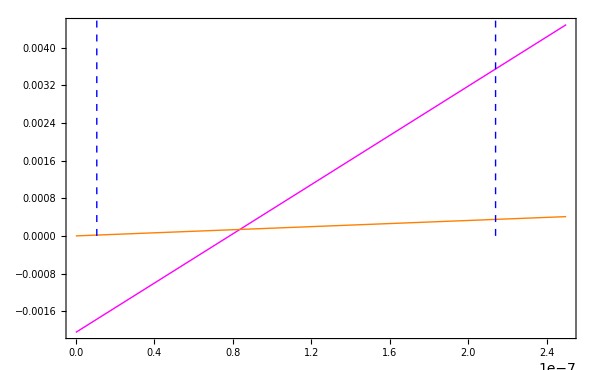

```mathematica
Module[{Ea,R,T0,H0,T,P,H,yeq,L,V,x0,xN,y1,yop},
Ea=5000;R=8.314;T0=298;H0=1640;(*atm/mole frac.*)
T=25;P=1;
H=H0*Exp[-Ea/R*(1/(T+273)-1/T0)];
yeq[x_]:=H/P*x;

L=1;V=3.82*^-5;
x0=2.14*^-7;xN=1.07*^-8;y1=3.55*^-3;
yop[x_]:=L/V*(x-x0)+y1;

Plot[{yop[x],yeq[x]},{x,0,2.5*^-7},PlotStyle->{{Thick,Magenta},{Thick,Orange}},
Frame->True,LabelStyle->{17,Black},ImageSize->600,
Epilog->{Thick,
{Dashed,Blue,Line[{{#,0},{#,0.026}}]&/@{x0,xN}}
}]
]
```